# Problem Set 2

## Problem 1

p_(x,y)(k, l) = c(k^2+l^2)
k : {-1, 0, 1, 3}
l: {-1, 2, 3}
∑_k  ∑_l  p_(x,y) = 1
89c = 1
c = 1/89

### Checking my work

```mathematica
pxy = c(k^2 + l^2)
soln = Solve[Sum[Sum[pxy, {k, {-1, 0, 1, 3}}], {l, {-1, 2, 3}}] == 1, c]
pxy/.soln/.{k->3, l->3}
```

### Part II

p_(x,y)(k, l) = 1/89(k^2+l^2)
(y,x) | -1 | 0 | 1 | 3
-1 | 2/89 | 1/89 | 2/89 | 10/89
2 | 5/89 | 4/89 | 5/89 | 13/89
3 | 10/89 | 9/89 | 10/89 | 18/89

P(X≤1,Y>2) = 29/89

## Problem 2

```mathematica
pxy = Piecewise[{{24 x y, 0 < x < 1 && 0 <y < 1&& x + y < 1}, {0, True}}]
ContourPlot[pxy, {x, 0, 2}, {y, 0, 2}]
```

Piecewise[{{24 x y, 0<x<1&&0<y<1&&x+y<1}, {0, True}}]

```mathematica
∫_(-∞)^∞ ∫_(-∞)^((1/2)-x) pxy ⅆy ⅆx
```

1/16

## Problem 3

```mathematica
cxy = Piecewise[{{(1 - Exp[-x^2])(1-Exp[-y^2]), x≥0 && y ≥0}, {0, True}}]
pxy = D[D[cxy, x], y]
```

Piecewise[{{(1-ⅇ^(-x^2)) (1-ⅇ^(-y^2)), x≥0&&y≥0}, {0, True}}]

Piecewise[{{4 ⅇ^(-x^2) x y-4 ⅇ^(-x^2-y^2) (-1+ⅇ^(y^2)) x y, x≥0&&y≥0}, {0, True}}]

## Problem 4

```mathematica
cxy = Piecewise[{{1-Exp[-x]-Exp[-y]+Exp[-x-y], x≥0&&y≥0}, {0, True}}]
pxy = D[D[cxy, x], y]
(1-∫_(-∞)^∞ ∫_(-∞)^(3-y) pxy ⅆx ⅆy)//FullSimplify
```

Piecewise[{{1-ⅇ^-x+ⅇ^(-x-y)-ⅇ^-y, x≥0&&y≥0}, {0, True}}]

Piecewise[{{ⅇ^-x-ⅇ^(-x-y) (-1+ⅇ^y), x≥0&&y≥0}, {0, True}}]

4/ⅇ^3

## Problem 5

```mathematica
pxy = Piecewise[{{24 y (1-x-y), x > 0 && y > 0 && x+ y < 1}, {0, True}}]
```

Piecewise[{{24 (1-x-y) y, x>0&&y>0&&x+y<1}, {0, True}}]

```mathematica
mx =∫_(-∞)^∞ pxy ⅆx
```

Piecewise[{{12 (y-2 y^2+y^3), 0<y<1}, {0, True}}]

```mathematica
my =∫_(-∞)^∞ pxy ⅆy
```

Piecewise[{{-4 (-1+x)^3, 0<x<1}, {0, True}}]

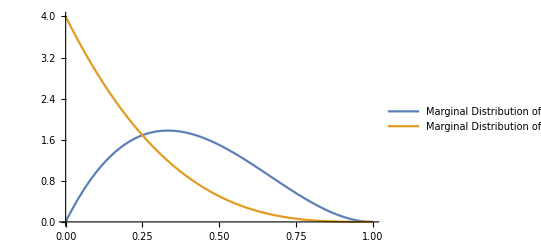

```mathematica
Plot[{
mx, 
my/.{x->y}}, 
{y, 0, 1}, 
PlotLegends->{"Marginal Distribution of y", "Marginal Distribution of x"}]
```

```mathematica
ProbabilityDistribution[2(1/3)^k,{k,1,∞}]
```

ProbabilityDistribution[2 3^-x,{x,1,∞}]

```mathematica
MomentGeneratingFunction[ProbabilityDistribution[2 3^-x,{x,1,∞}],t]
```

-(2 ⅇ^t)/(3 t-Log[27])

```mathematica
firstMoment = D[(-(2 ⅇ^t)/(3 t-Log[27])), t]
```

(6 ⅇ^t)/(3 t-Log[27])^2-(2 ⅇ^t)/(3 t-Log[27])

```mathematica
secondMoment = D[((6 ⅇ^t)/(3 t-Log[27])^2-(2 ⅇ^t)/(3 t-Log[27])), t]
```

-(36 ⅇ^t)/(3 t-Log[27])^3+(12 ⅇ^t)/(3 t-Log[27])^2-(2 ⅇ^t)/(3 t-Log[27])